```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
std=StandardDeviation@portfolio[[All,2]];
return=Last@portfolio[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
end//DateString
```

Tue 20 Jun 2017

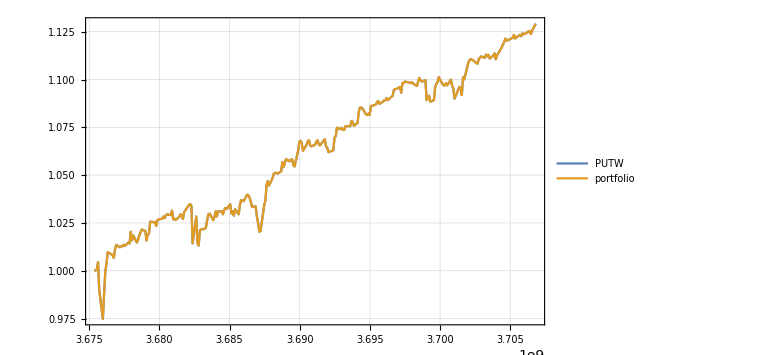
{-Graphics-,return | 1.1292
std | 0.037706
r/s | 29.9475}

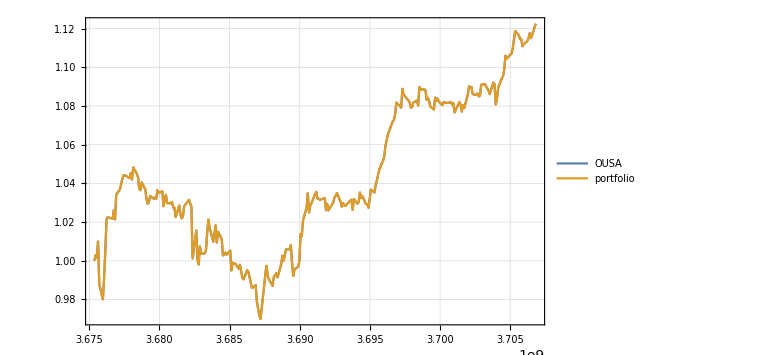
{-Graphics-,return | 1.12258
std | 0.0380377
r/s | 29.5124}

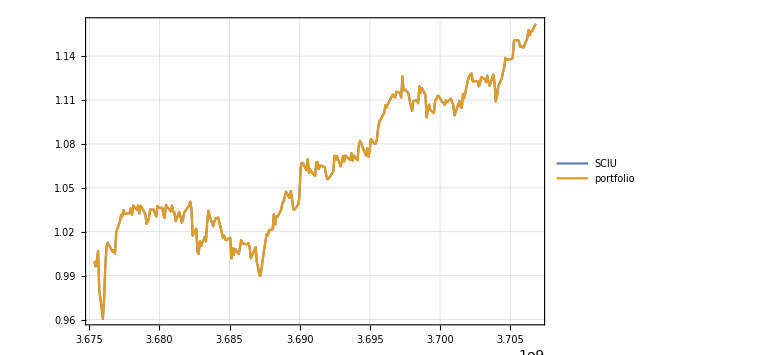
{-Graphics-,return | 1.16219
std | 0.0468712
r/s | 24.7955}

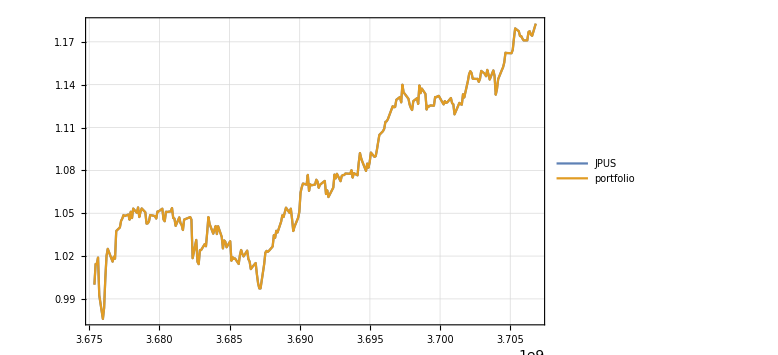
{-Graphics-,return | 1.18274
std | 0.0510782
r/s | 23.1554}

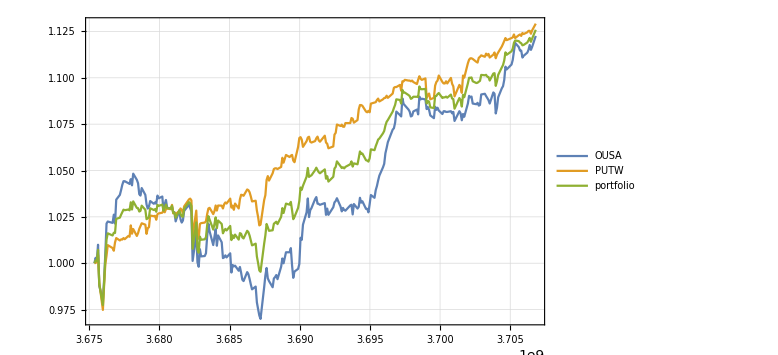
{-Graphics-,return | 1.12589
std | 0.036107
r/s | 31.1821}

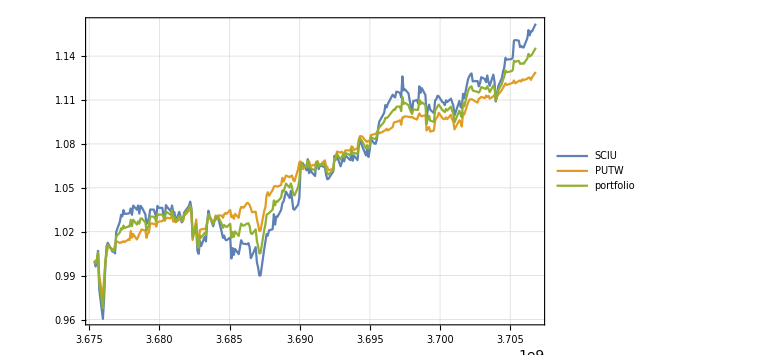
{-Graphics-,return | 1.1457
std | 0.041854
r/s | 27.3736}

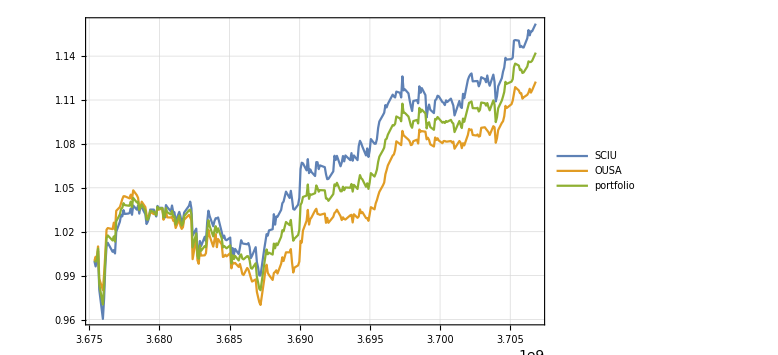
{-Graphics-,return | 1.14239
std | 0.0417718
r/s | 27.3483}

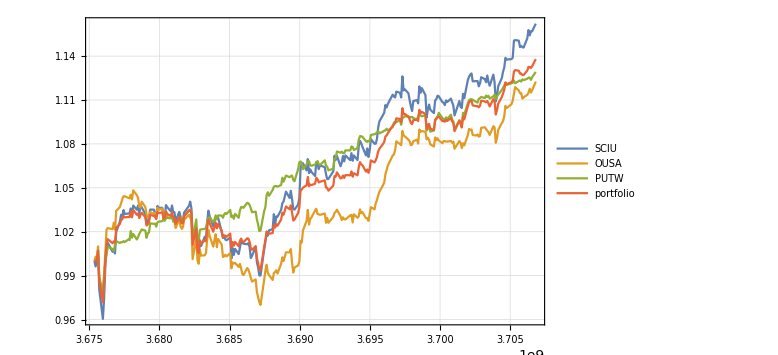
{-Graphics-,return | 1.13799
std | 0.0396315
r/s | 28.7143}

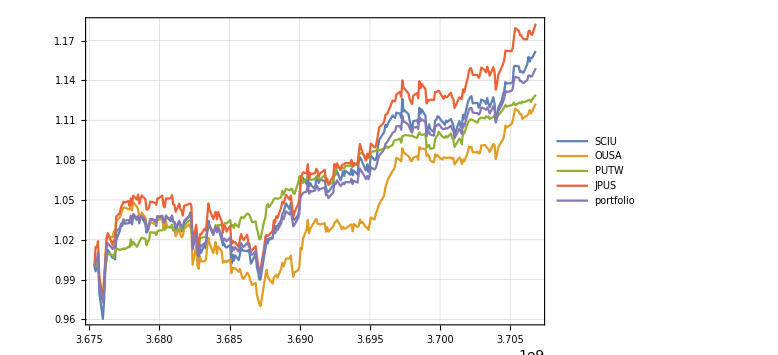
{-Graphics-,return | 1.14918
std | 0.0424758
r/s | 27.0549}

```mathematica
PortfolioChart[{"PUTW"},start1,end]
PortfolioChart[{"OUSA"},start1,end]
PortfolioChart[{"SCIU"},start1,end]
PortfolioChart[{"JPUS"},start1,end]
PortfolioChart[{"OUSA","PUTW"},start1,end]
PortfolioChart[{"SCIU","PUTW"},start1,end]
PortfolioChart[{"SCIU","OUSA"},start1,end]
PortfolioChart[{"SCIU","OUSA","PUTW"},start1,end]
PortfolioChart[{"SCIU","OUSA","PUTW","JPUS"},start1,end]
```

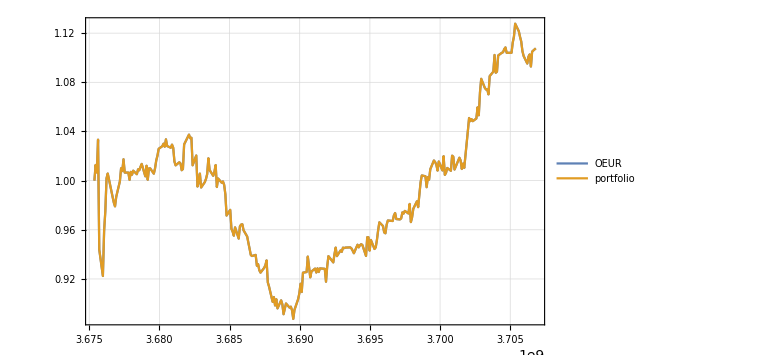
{-Graphics-,return | 1.10763
std | 0.056392
r/s | 19.6416}

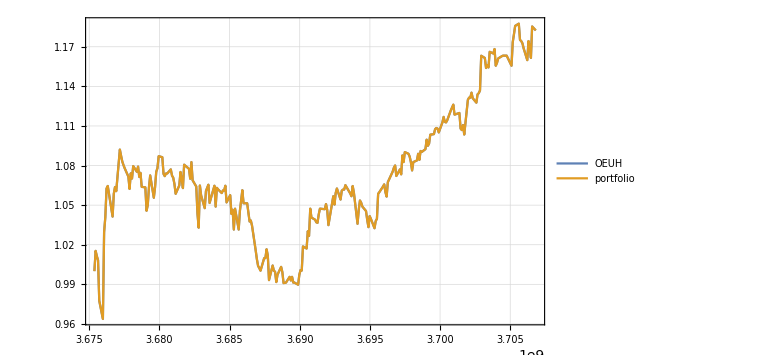
{-Graphics-,return | 1.18241
std | 0.0488486
r/s | 24.2056}

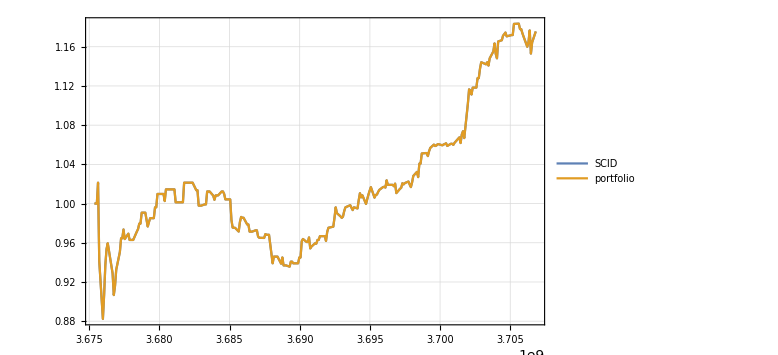
{-Graphics-,return | 1.1756
std | 0.0678854
r/s | 17.3174}

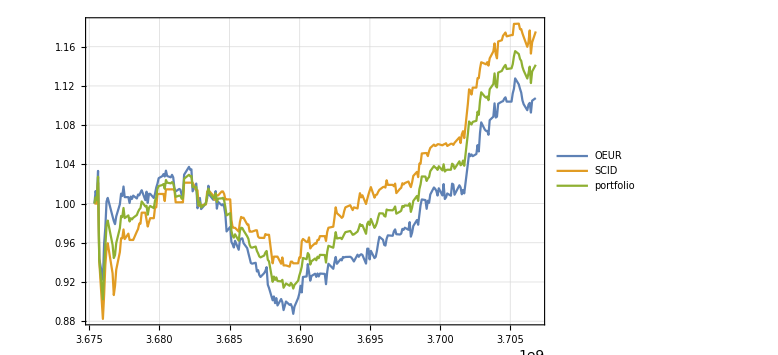
{-Graphics-,return | 1.14161
std | 0.0598916
r/s | 19.0613}

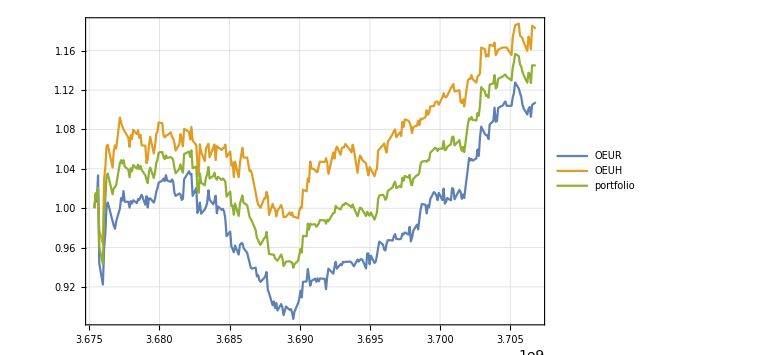
{-Graphics-,return | 1.14502
std | 0.051249
r/s | 22.3423}

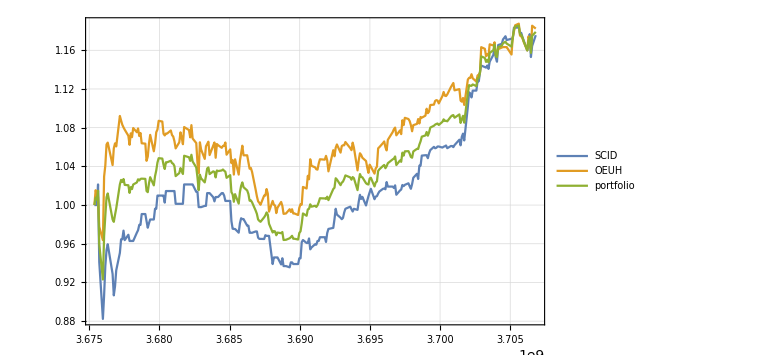
{-Graphics-,return | 1.179
std | 0.0571525
r/s | 20.629}

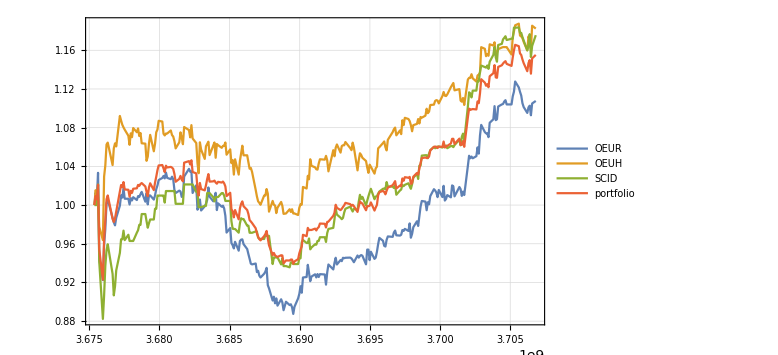
{-Graphics-,return | 1.15521
std | 0.0555226
r/s | 20.8061}

```mathematica
PortfolioChart[{"OEUR"},start1,end]
PortfolioChart[{"OEUH"},start1,end]
PortfolioChart[{"SCID"},start1,end]
PortfolioChart[{"OEUR","SCID"},start1,end]
PortfolioChart[{"OEUR","OEUH"},start1,end]
PortfolioChart[{"SCID","OEUH"},start1,end]
PortfolioChart[{"OEUR","OEUH","SCID"},start1,end]
```

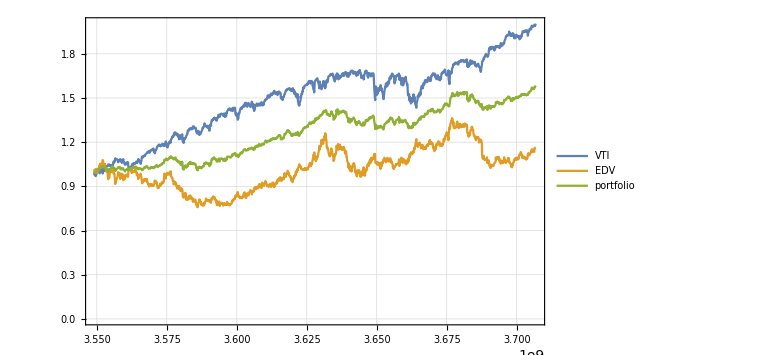
{-Graphics-,return | 1.5828
std | 0.175509
r/s | 9.01833}

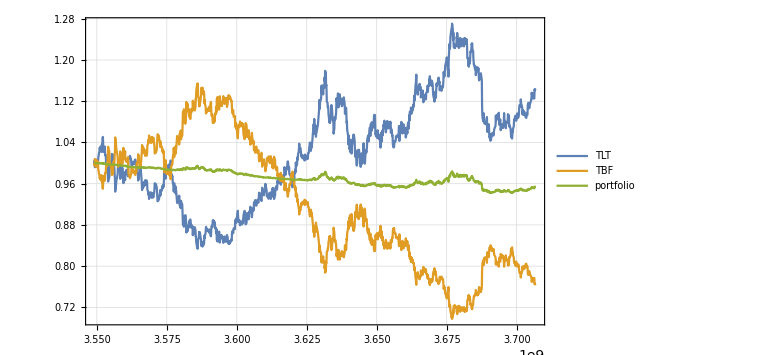
{-Graphics-,return | 0.953811
std | 0.0156823
r/s | 60.821}

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
PortfolioChart[{"TLT","TBF"},start,end]
```

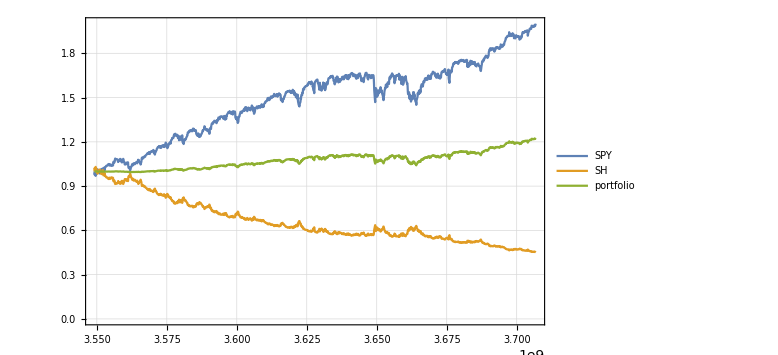
{-Graphics-,return | 1.22611
std | 0.0574856
r/s | 21.329}

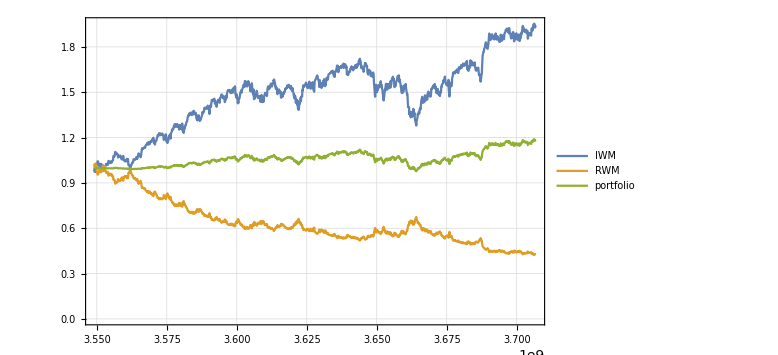
{-Graphics-,return | 1.18409
std | 0.0487643
r/s | 24.2818}

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

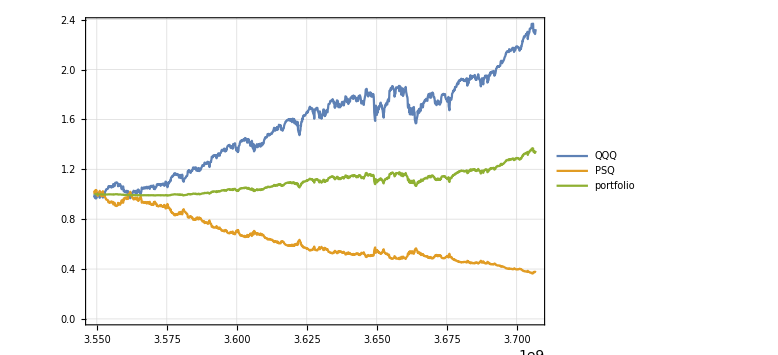
{-Graphics-,return | 1.34756
std | 0.0895184
r/s | 15.0535}

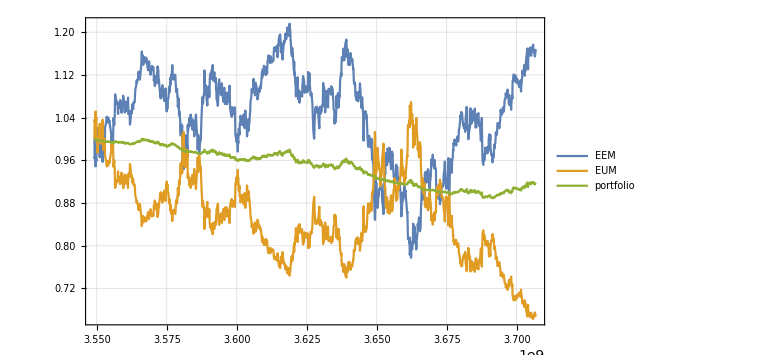
{-Graphics-,return | 0.917602
std | 0.03458
r/s | 26.5357}

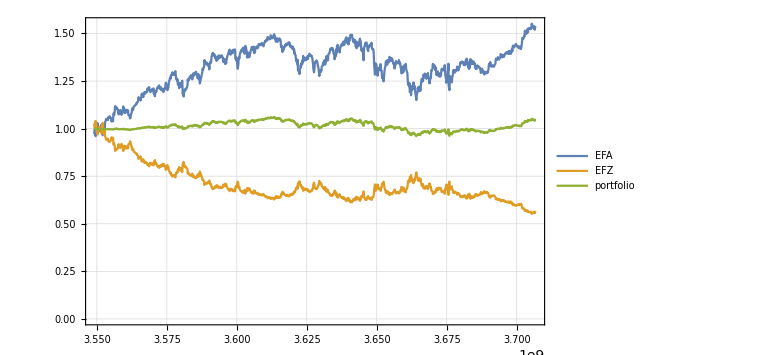
{-Graphics-,return | 1.04743
std | 0.0222886
r/s | 46.9941}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

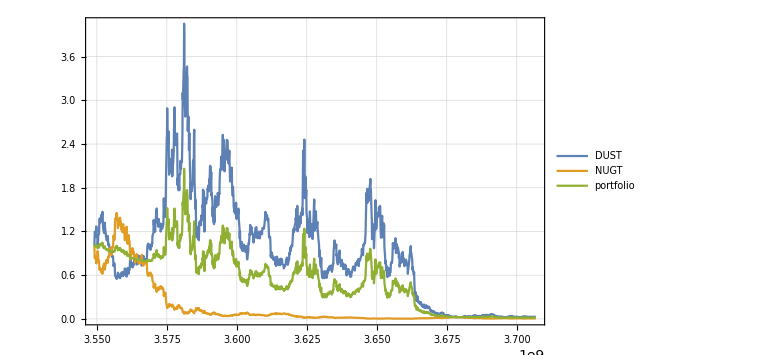
{-Graphics-,return | 0.018438
std | 0.395129
r/s | 0.0466632}

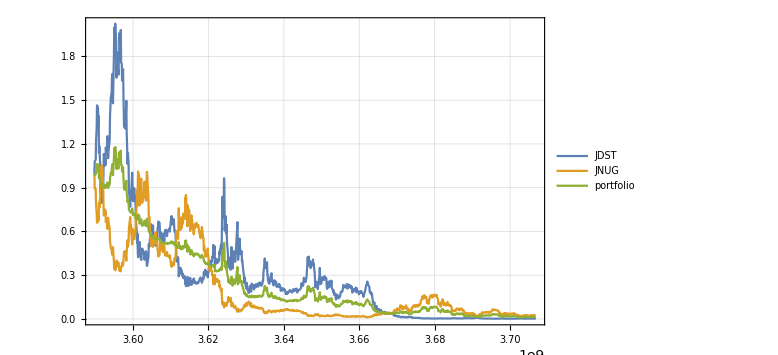
{-Graphics-,return | 0.0124949
std | 0.284882
r/s | 0.0438599}

```mathematica
PortfolioChart[{"DUST","NUGT"},start,end]
PortfolioChart[{"JDST","JNUG"},start,end]
```